# Population annealing analysis - fixed

## All trials: N = 8, R = 12, M = 10, K = 10, β = 10, J = 3, C = 4, S = 5, L = 6

N = number of spins
R = initial population size
M = number of MC sweeps per temperature step
K = number of temperature steps
β = target beta
J = J_{ij} matrix seed
C = MC sweep seed
S = initial spin seed
L = randfrom seed

## Import Relevant Files

```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
trials=4;
steps=Range[1,10];
energies=Range[1,trials];
For[i=1,i≤trials,i++,
Evaluate[Symbol["energies"<>ToString[i]]]=Import["energies_t"<>ToString[i]<>".csv","CSV"];
energies⟦i⟧=Evaluate[Symbol["energies"<>ToString[i]]];
]
```

## Create Histograms

```mathematica
trial1=Manipulate[Histogram[energies⟦1⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 1: 1 Thread",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦1⟧]-1,1}];
trial2=Manipulate[Histogram[energies⟦2⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 2: 2 Threads",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦2⟧]-1,1}];
trial3=Manipulate[Histogram[energies⟦3⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 3: 3 Threads",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦3⟧]-1,1}];
trial4=Manipulate[Histogram[energies⟦4⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 4: 4 Threads",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦4⟧]-1,1}];
```

## Display Histograms

```mathematica
Grid[{{trial1,trial2},{trial3,trial4}}]
```

| 
 |

## Analyze Runtimes

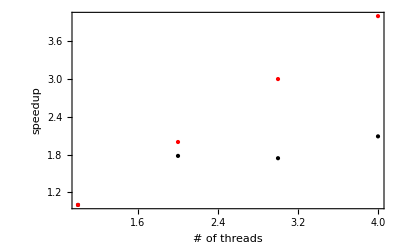

2.08949

```mathematica
threads={1,2,3,4};
times={0.024259,0.013634,0.013922,0.011610};
speedup=0.024259/times;
speedupPlot=ListPlot[Transpose[{threads,speedup}],PlotStyle->{Black,PointSize[Large]}];
idealPlot=ListPlot[Transpose[{threads,threads}],PlotStyle->{Red,PointSize[Large]}];
Show[speedupPlot,idealPlot,Frame->True,PlotRange->All,FrameLabel->{"# of threads","speedup"}]
speedup[[4]]
```